Let us consider two vector fields:

```mathematica
(*Two vector fields on R^2: X = {x y, x^2} and Y = {0, y}*)
X={x y,x^2};Y={0,y};
```

Here the standard basis vector fields are ∂/∂x and ∂/∂y

let us plot these vector fields:

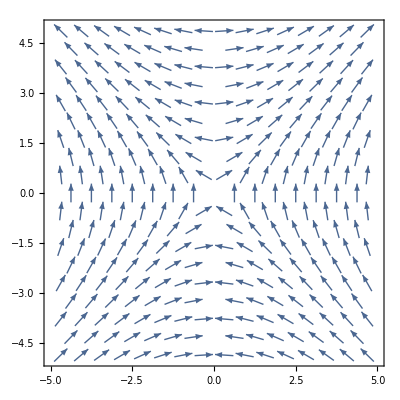
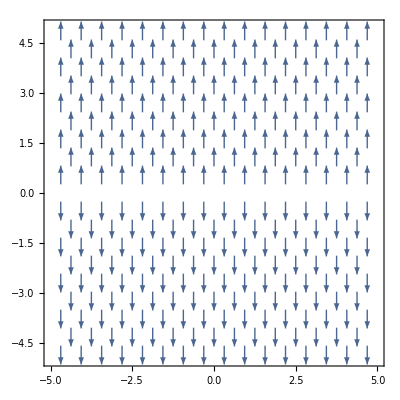

```mathematica
(*Plot the two vector fields side by side*)
VectorPlot[#,{x,-5,5},{y,-5,5},VectorColorFunction->None]&/@{X,Y}
```

We consider vectors at a particular point, say (1,1)

```mathematica
(*Evaluate both fields at the point p = (1,1)*)
p={1,1};{Xp,Yp}={X,Y}/.MapThread[Rule,{{x,y},p}]
```

{{1,1},{0,1}}

The vector Xp is denoted in red and Yp is denoted in blue color.

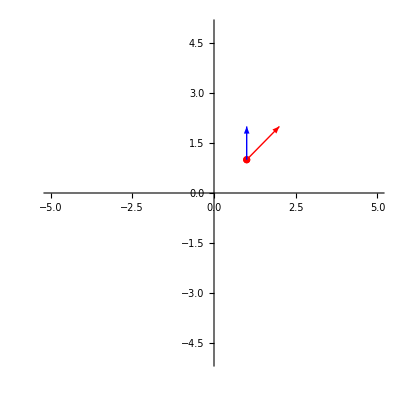

```mathematica
(*Draw Xp (red) and Yp (blue) as arrows based at p*)
Show[ListPlot[{p},PlotRange->{{-5,5},{-5,5}},PlotStyle->Red],
Graphics[{Red,Arrow[{p,p+Xp}]},PlotRange->{{-5,5},{-5,5}}],
Graphics[{Blue,Arrow[{p,p+Yp}]},PlotRange->{{-5,5},{-5,5}}],AspectRatio-> 1]
```

Now consider a map f:R^2 -> R^2 given by

```mathematica
(*A linear map f:R^2 -> R^2, f(x,y) = (x+y, x-y); its Jacobian is the symmetric matrix {{1,1},{1,-1}}*)
f[{x_,y_}]:={x+y,x-y}
```

The point P gets mapped to fp

```mathematica
(*Image of the point p under the map f*)
fp = f[p]
```

{2,0}

Let us see how the vectors Xp and Yp are pushed forward by this map.

```mathematica
(*Pushforward of the vectors at p: apply the Jacobian J of f at p. Pushforward of v is J . v*)
Jp=Table[D[i,j],{i,f[{x,y}]},{j,{x,y}}]/.MapThread[Rule,{{x,y},p}];{XXp,YYp}={Jp.Xp,Jp.Yp}
```

{{2,0},{1,-1}}

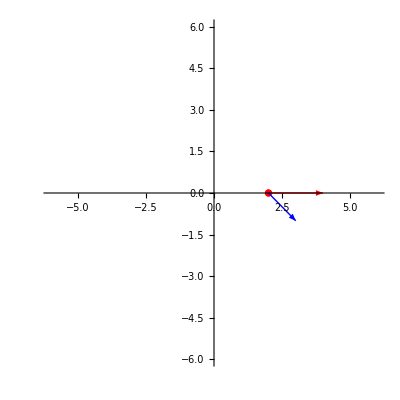

```mathematica
(*Draw the pushed-forward vectors XXp (red) and YYp (blue) based at f(p)*)
Show[ListPlot[{fp},PlotRange->{{-6,6},{-6,6}},PlotStyle->Red],
Graphics[{Red,Arrow[{fp,fp+XXp}]},PlotRange->{{-6,6},{-6,6}}],
Graphics[{Blue,Arrow[{fp,fp+YYp}]},PlotRange->{{-6,6},{-6,6}}],AspectRatio-> 1]
```

We can pushforward the vector fields X and Y as follows, denoting (x1,y1) as the coordinates of the image space

```mathematica
(*Pushforward of the whole fields (J . field), then rewrite x,y in the image coordinates x1,y1*)
Jf=Table[D[i,j],{i,f[{x,y}]},{j,{x,y}}];{newX,newY}=Simplify[{Jf.X,Jf.Y}/.Flatten[Solve[{x+y==x1,x-y==y1},{x,y}]]]
```

{{1/2 x1 (x1+y1),-1/2 y1 (x1+y1)},{(x1-y1)/2,1/2 (-x1+y1)}}

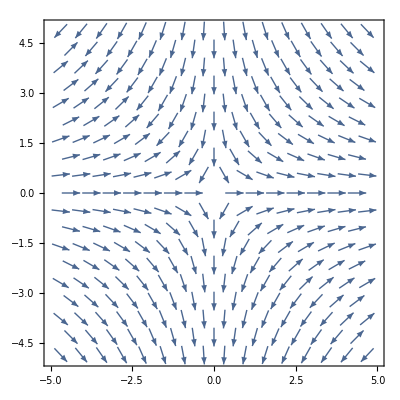
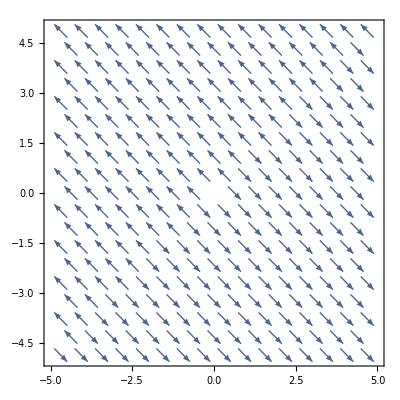

```mathematica
(*Plot the pushed-forward vector fields in the image coordinates x1,y1*)
VectorPlot[#,{x1,-5,5},{y1,-5,5},VectorColorFunction->None]&/@{newX,newY}
```